```mathematica
**Find the equation of the circle, which passes thtough the points of intersection points of the two circles  x^2+y^2-4=0and x^2+y^2-2x-4y +4 =0and touches the line x+2y =0.(ch--6, ex--07)
```

```mathematica
Exit[]
```

```mathematica
k=Collect[x^2+y^2-4+λ(x^2+y^2-2x-4y +4 ),{x,y}]==0
```

-4+4 λ-2 x λ-4 y λ+x^2 (1+λ)+y^2 (1+λ)==0

```mathematica
g=λ;f=2λ;c=-4+4λ;
s=Solve[(√(g^2+f^2-c))^2==((-g-2f)/(√(1+4)))^2,λ];
k/.s[[1]]
```

-2 x+2 x^2-4 y+2 y^2==0

```mathematica
g1=ContourPlot[{ x^2+y^2-4==0,x^2+y^2-2x-4y +4 ==0,x+2y ==0},{x,-3,3},{y,-3,3}]
```

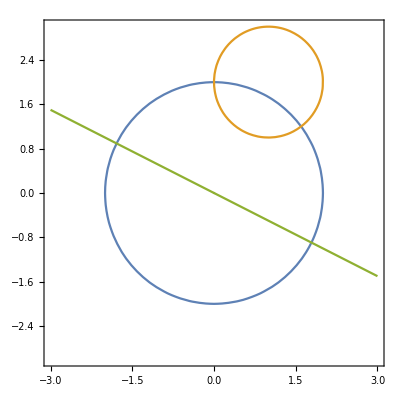

```mathematica
Show[g1,Axes->True]
```

-Graphics-

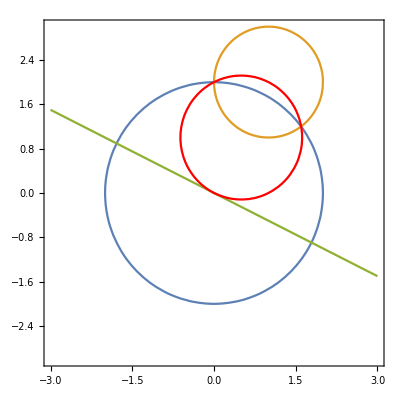

```mathematica
g2=ContourPlot[-2 x+2 x^2-4 y+2 y^2==0,{x,-3,3},{y,-3,3},ContourStyle->Red];
Show[g1,g2,Axes->True]
```

```mathematica
Exit[]
```

```mathematica
**Example -8
```

```mathematica
a=Pi/4;x^2-y^2==5./.{x->x*Cos[a]-y*Sin[a],y->x*Sin[a]+y*Cos[a]}//Simplify
```

-2 x y==5.

```mathematica
Exit[]
```

```mathematica
** Example 9
```

```mathematica
k=11 x^2-4x*y+14 y^2-58x-44y+126==0;
s=Solve[{X==(2x+y-8)/(√(4+1)),Y==(x-2y+1)/(√(1+4))},{x,y}];
k/.s[[1]]//Simplify
```

2 X^2+3 Y^2==1

```mathematica
Exit[]
```

```mathematica
**Example 10
```

```mathematica
k=3 x^2-4 y^2-6x-8y-10;a=3;b=-4;
h=0;
s=Solve[D[k,x]==0&&D[k,y]==0,{x,y}]
```

{{x→1,y→-1}}

```mathematica
k==0/.{x->1+x,y->-1+y}//Simplify
```

3 x^2==9+4 y^2

```mathematica
Exit[]
```

```mathematica
** Example 11
```

```mathematica
(*ex.5.Find the equation to the circle passing through the point (1,-2) and (4,-3) and which has its centre  in the straight line 3x=4y=7*)
```

```mathematica
h[x_,y_]:=x^2+y^2+2g*x+2f*y+c==0
s=Solve[h[1,-2]&&h[4,-3]&&3(-g)+4(-f)==7,{g,f,c}];
h[x,y]/.s[[1]]//Simplify//Expand
```

55+15 x^2+18 y+15 y^2==94 x

```mathematica
(*ex.10..Write Mathematica Code to remove the first degree terms of the equation 3 x^2-4 y^2-6x-8y-10=0 *)
k:=3 x^2-4 y^2-6x-8y-10
a=3;b=-4;h=0;
s=Solve[D[k,x]==0&&D[k,y]==0,{x,y}]
```

{{x→1,y→-1}}

```mathematica
k==0/.{x->1+x,y->-1+y}//Simplify
```

3 x^2==9+4 y^2

```mathematica
Exit[]
(*Transform the equation 17 x^2+18x*y-7 y^2-16x-13y-18=0 to one in which there are no term involving x,y and xy,both sets of axees being rectangular.*)
k:=17 x^2+18x*y-7 y^2-16x-13y-18
a=17;b=-7;h=18/2;
s=Solve[D[k,x]==0&&D[k,y],{x,y}];
α=s[[1,1,2]];β=s[[1,2,2]];
t=1/2 ArcTan[(2h)/(a-b)];
k==0/2.{x->α+xCos[t]-ySin[t],y->β+xSin[t]+yCos[t]}//Simplify
```

```mathematica
(*Ex.15. Show that the following equation represent a pair of straight lies.  find the point of intersection of two lines plot their colour diagram 2 x^2+5xy+2 y^2+10x+5y=0*)
k=2 x^2+5xy+2 y^2+10x+5y=0
a=2;b=2;c=0;h=5/2;g=5;f=5/2;
d=a*b*c+2f*g*h-af^2-bg^2-ch^2;h1=ab-h^2; c1=a+b;If[d==0,Print["Pair of straight line"],Print["Pair of not straight line"]]
```

Set::write: Tag Plus in 10\ x + 2\ x^2 + 5\ xy + 5\ y + 2\ y^2 is Protected.

0

If[abc-af^2-bg^2-ch^2+2 fgh==0,Print[Pair of straight line],Print[Pair of not straight line]]

```mathematica
Print["The point of intersection is(",α=(h*f-b*g)/h1,",",β=(g*h-a*f)/h1,")"]
```

The point of intersection is(-15/(4 (-25/4+ab)),15/(2 (-25/4+ab)))

```mathematica
L=Factor[k]
```

0

Set::write: Tag Plus in 10 is Protected. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/General/write",
ButtonNote->"Set::write"]

0

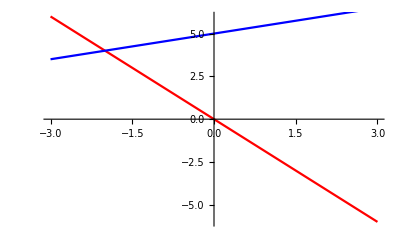

```mathematica
g1=Plot[(-2x),{x,-3,3},PlotStyle->Red];
g2=Plot[(5+x/2),{x,-3,3},PlotStyle->Blue];
Show[g1,g2]
```

```mathematica
Exit[]
```

```mathematica
(*Ex.19.Show that the equation 6 x^2-5xy-6 y^2+14x+5y+4=0 represent a pair of straight lines. Find the point of intersection of the two lines. Calculate the area of the triangule region bounded by the two lines and y-exis.*)
k=6 x^2-5xy-6 y^2+14x+5y+4
a=6;h=-5/2;b=-6;g=7;f=5/2;c=4;del=a*b*c+2f*g*h-a*f^2-b*g^2-c*h^2;h1=a*b-h^2;If[del==0,Print["Pair of s.lines"],Print["no Pair of s.lines"]]
```

4+14 x+6 x^2-5 xy+5 y-6 y^2

Pair of s.lines

```mathematica
L=Factor[k];
Print["the lines sare",L1=L[[1]]==0,"amd",L2=L[[2]]==0]
```

Part::partd: Part specification k ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification k ⟦ 2 ⟧ is longer than depth of object.

the lines sarek⟦1⟧==0amdk⟦2⟧==0

```mathematica
A2=Solve[x==0&&L1,{x,y}]
A3=Solve[x==0&&L2{x,y}]
```

{}

Solve::naqs: x == 0 && {x\ (14\ x == 0), y\ (14\ x == 0)} is not a quantified system of equations and inequalities.

Solve[x==0&&{x (14 x==0),y (14 x==0)}]

```mathematica
Print["theireeais",0.5Abs[Det[{{0,4/3,1},{0,-1/2,1},{-11/13,10/13,1}}]],"units"]
```

theireeais0.775641units

```mathematica
Exit[]
```

```mathematica
A={3,3,8}'B={-3-7,6};
a1={3,-1,1};a2={-3,2,4};
P=A+ra1;Q=B+r1a2;
s=Solve[a1.(P-Q)==0&&a2.(P-Q)==0,{r,r1}]
```

Set::write: Tag Times in {-10, 6} is Protected.

Dot::dotsh: Tensors {3, -1, 1} and {-r1a2 + ra1, -r1a2 + ra1} have incompatible shapes.

Dot::dotsh: Tensors {-3, 2, 4} and {-r1a2 + ra1, -r1a2 + ra1} have incompatible shapes.

{}

```mathematica
(*Ex.24.Find the length and equation of shortest distance between the lines (x-1)/2=(y-2)/3=(z-4)/4 and(x-2)/2=(y-4)/4=(z-5)/5*)
x1=1;y1=2;z1=4;x2=2;y2=4;z2=5;
l1=2;m1=3;n1=4;l2=2;m2=4;n2=5;
ang=ArcSin[];
l=(m1*n2-m2*n1)/Sin[ang];
m=(n1*l2-n2*l1)/Sin[ang];
        n=(l1*m2-l2*m1)/Sin[ang];
	SD=1*(x2-x1)+m*(y2-y1)+n*(z2-z1)//Simplify-1
A1=({{x-x1,y-y1,z-z1},{l1,m1,n1},{l,m,n}});
SD1=Det[A1]//Simplify;
A2=({{x-x1,y-y1,z-z1},{l2,m2,n2},{l,m,n}});
SD2=Det[A2]//Simplify;
SD1==0
SD2==0
```

ArcSin::argx: ArcSin called with 0 arguments; 1 argument is expected.

(-1+Simplify)[1-2 Csc[ArcSin[]]]

(6+14 x-8 y-z) Csc[ArcSin[]]==0

9 (2 x-y) Csc[ArcSin[]]==0

```mathematica
Exit[]
```

```mathematica
(*Show that 2 x^2+4xy-3 y^2+x+10y-3=0 represents a pair of straight lines, Find the equation of lines the angle between them. also find the area of the triangle formed by these two lines and the axis of y. Plot the grap*)
f[x_,y_]:=2 x^2+5x*y-3 y^2+x+10y-3=0;
a=2;h=5/2;b=-3;g=1/2;f=5;c=-3;
del=a*b*c+2f*g*h-a*f^2-b*g^2-c*h^2
```

SetDelayed::write: Tag Integer in 5[x_, y_] is Protected.

0

```mathematica
Factor[2 x^2+5x*y-3 y^2+x+10y-3]
```

(3+2 x-y) (-1+x+3 y)

```mathematica
p1=ContourPlot[2 x^2+5x*y-3 y^2+x+10y-3==0,{x,-5,5},{y,-5,5}]
```

```mathematica
(*Ex.29.Find the unite vector perperdicular to both a=2i-6j-3k and b=4i+3j-k.*)
a={2,-6,-3};
b={4,3,-1};
c=Cross[a,b]
```

{15,-10,30}

```mathematica
univector=c/Norm[c]
```

{3/7,-2/7,6/7}

```mathematica
(*Ex.30.Identify the conic x^2+2xy+y^2-2x-1=0 Reduce the equation to the standerd from and discuss the nature of this conic. Sketch the graph.*)
a=1;h=1;b=1;g=-1;f=0;c=-1;
Δ=a*b*c+2f*g*h-a*f^2-b*g^2-c*h^2
a*b-h^2
```

-1

0

```mathematica
Solve[2k+2+2k==0,k]
```

{{k→-1/2}}

```mathematica
(*Vertex*)
X=(4x-4y+5)/(4 √2);Y=(2x+2y-1)/(2 √2);
Solve[{X==0,Y==0},{x,y}]
```

{{x→-3/8,y→7/8}}

```mathematica
(*Focus*)
a=1/(4 √2)
Solve[{X==a,Y==0},{x,y}]
```

1/(4 √2)

{{x→-1/4,y→3/4}}

```mathematica
(*Lenth of the latus rectum=4a*)
4a
```

1/(√2)

```mathematica
(*Equation of the directrix x=-a*)
Simplify[X==-a]
```

3+2 x==2 y

```mathematica
(*Equation of the latus rectum x=a*)
Simplify[X==a]
```

1+x==y

```mathematica
(*Equation of the axix y=0*)
Simplify[Y==0]
```

2 (x+y)==1

```mathematica
(*Equation of tengent at the vertex x=0*)
Simplify[X==0]
```

5+4 x==4 y

```mathematica
(*For Figure*)
ContourPlot[x^2+y^2+2x*y+y^2-2x-1==0,{x,-5,5},{y,-5,5}]
```

```mathematica
ContourPlot[{x^2+y^2+2x*y+y^2-2x-1==0,2x+2y-1==0,4x_4y+5==0,2x-2y+3==0},{x,-5,5},{y,-5,5}]
```